```mathematica
(* first iterate *)
```

```mathematica
(* every rational point on this curve gives (newly) reducible f *)
Plot3D[{Sqrt[-m-g],-Sqrt[-m-g]},{m,-10,10},{g,-10,10},PlotRange->All]
```

-Graphics3D-

```mathematica
(* or, given y and m, γ is -y^2-m *)
```

```mathematica
firstImages={};
Do[Do[
γ=-y^2-m;
AppendTo[firstImages,{m,γ}];
,{y,0,10}],{m,-50,50}]
```

```mathematica
RFI={};
Do[Do[
f[x_]:=(x-γ)^2+γ+m;
If[¬IrreduciblePolynomialQ[f[x]],
AppendTo[RFI,{m,γ}];
];
,{m,-100,100}],{γ,-100,100}]
```

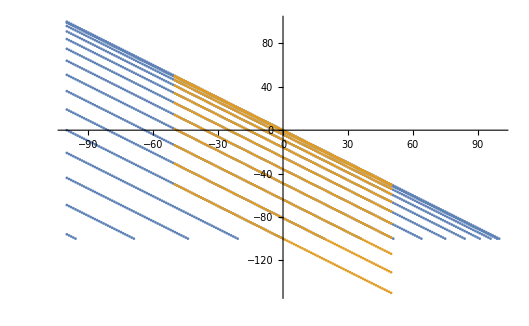

```mathematica
ListPlot[{RFI,firstImages}](* no surprise, they coincide. So the family of reducible 1st iterates is like a 2-dimensional family, with parameters y and γ *)
```

```mathematica
(* Note: there are no reducible first iterates above the line γ = -m, because if γ > -m then 0 > -γ-m *)
```

```mathematica
(* second iterate *)
```

```mathematica
(* image of parametrization of newly reducible f^2 *)
f2gamma[s_,r_]:=s^2/4-r^2+r^2/s^2;
f2m[s_,r_]:=-s^2/4-r^2/s^2;
```

```mathematica
NRSI={};
Do[Do[
f[x_]:=(x-γ)^2+γ+m;
If[IrreduciblePolynomialQ[f[x]]&&¬IrreduciblePolynomialQ[f[f[x]]],
AppendTo[NRSI,{m,γ}];
];
,{m,-30,30,1/2}],{γ,-30,30,1/2}]
```

```mathematica
ListPlot[NRSI](* some newly reducible second iterates in this range *)
```

```mathematica
Images={};
Do[Do[Do[
If[i==1,im=1,im=ⅈ];
r=Sqrt[rsquared];
AppendTo[Images,{f2m[s,r*im],f2gamma[s,r*im]}];
,{i,0,1}],{s,1/10,10,1/10}],{rsquared,1,500,1}];
```

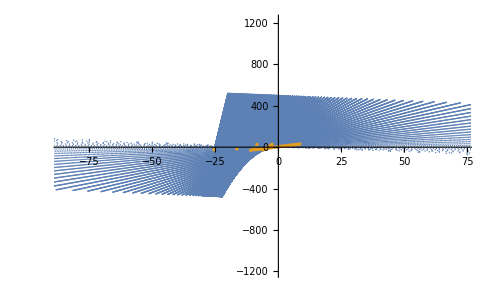

```mathematica
ListPlot[{Images,NRSI},PlotStyle->{PointSize[.002],PointSize[.005]}] (* Images of the r, s above, plotted with the newly reducible 2nd iterates we found earlier. It looks like they coincide, and again we have a 2-dimensional family (r and s) *)
```

```mathematica
Images2={};
Do[Do[Do[
If[i==1,im=1,im=ⅈ];
r=Sqrt[rsquared];
AppendTo[Images2,{f2m[s,r*im],f2gamma[s,r*im]}];
,{i,0,1,1}],{s,1/1000,10,1/10}],{rsquared,1,100,1}];
```

```mathematica
Images2[[1;;50]]//MatrixForm
```

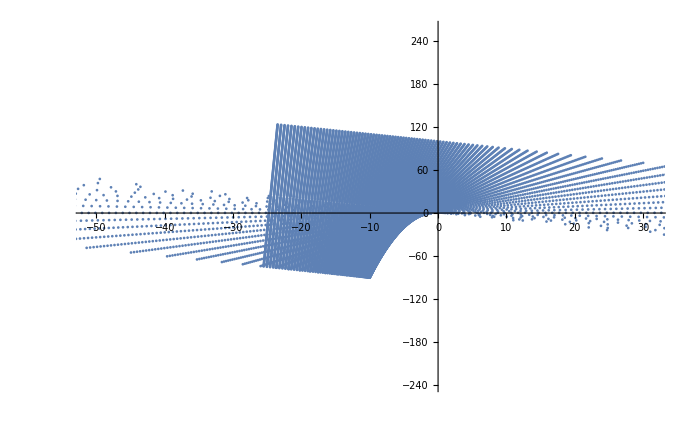

```mathematica
ListPlot[Images2]
```

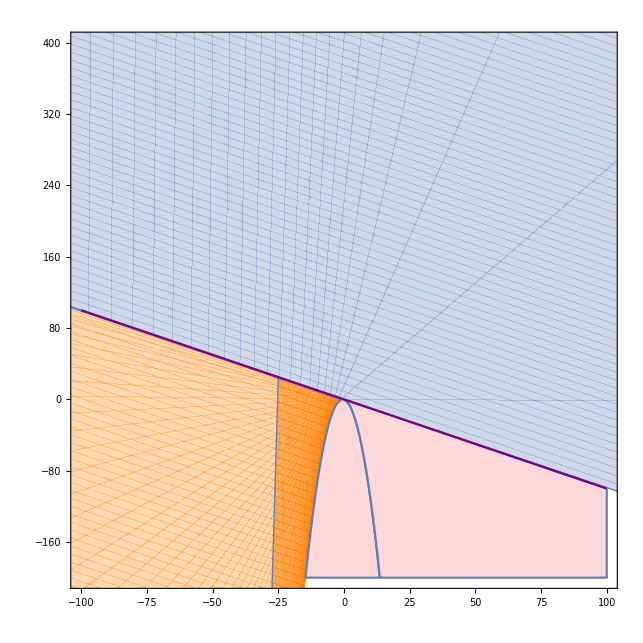

```mathematica
Show[
ParametricPlot[{f2m[s,Sqrt[r]*ⅈ],f2gamma[s,Sqrt[r]*ⅈ]},{r,1/10,1000},{s,1/10,100},PlotRange->{{-100,100},{-200,400}},AspectRatio->1,MaxRecursion->3],
ParametricPlot[{f2m[s,Sqrt[r]],f2gamma[s,Sqrt[r]]},{r,1,1000},{s,1/10,10},MaxRecursion->3,PlotStyle->Orange],
RegionPlot[0>m^2+γ+m,{m,-100,100},{γ,-200,200},PlotStyle->LightRed,MaxRecursion->3],
RegionPlot[0>2(-m+Sqrt[m^2+γ+m])&&0>2(-m-Sqrt[m^2+γ+m]),{m,-100,100},{γ,-200,200},PlotStyle->LightRed,MaxRecursion->4],
Plot[-m,{m,-100,100},PlotStyle->Purple]
](* red regions mark where s would be complex, so there are no newly reducible 2nd iterates there *)
```

```mathematica
(* third iterate *)
```

```mathematica
(* given rational (r,s=d) in A^2, returns (m,y) that is a solution to S *)
ϕ[r_,s_]:={(-4-4 r-r^2-4 s^2-2 r s^2+s^4)/(8 r),(-4+r^2-4 s^2+s^4)/(2 r)};
(* given m and d, return gamma *)
gamma[m_,d_]:=Sqrt[2 d^4+8m d^2+16 m^2+16m](-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
```

```mathematica
(* images of rectangles of various sizes *)
rmin=-5;
rmax=5;
smin=-5;
smax=5;
Show[ParametricPlot[{ϕ[r,d][[1]],gamma[ϕ[r,d][[1]],d]},{r,rmin,rmax},{d,smin,smax},PlotRange->{{-10,10},{-60,40}},AspectRatio->1,MaxRecursion->4],
Plot[-m,{m,-30,30}]]
```

```mathematica
NRTI={};
Do[Do[
If[r≠0,
AppendTo[NRTI,{ϕ[r,s][[1]],gamma[ϕ[r,s][[1]],s]}];
];
,{r,-120,120,1}],{s,-5,5,1/10}];
```

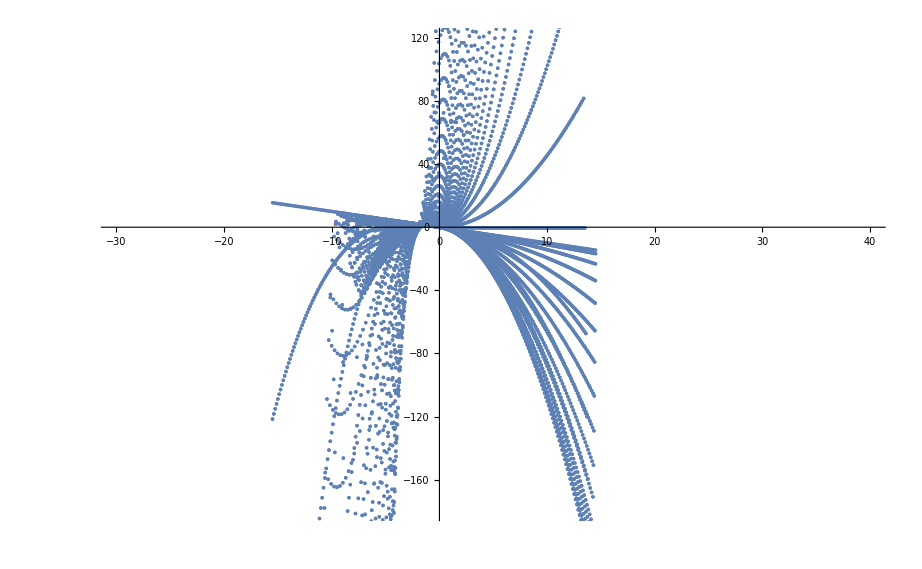

```mathematica
Show[ListPlot[NRTI,PlotRange->{{-30,40},{-180,120}}]]
```

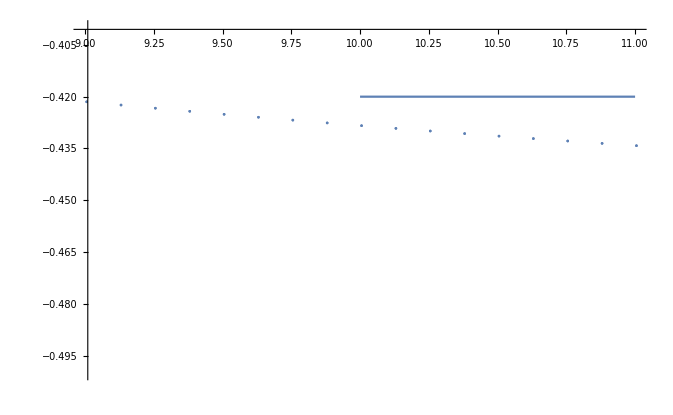

```mathematica
Show[ListPlot[NRTI,PlotRange->{{9,11},{-.5,-.4}}],Plot[-m,{m,-30,40}],Plot[-42/100 ,{m,10,11}]]
```

```mathematica
Show[
ParametricPlot[{ϕ[r,d][[1]],gamma[ϕ[r,d][[1]],d]},{r,-1,100},{d,0,10},PlotRange->{{-10,10},{-60,40}},AspectRatio->1,MaxRecursion->4]
,
ListPlot[NRTI,PlotRange->{{-10,10},{-60,40}},PlotStyle->Orange]
]
```

-Graphics-

```mathematica
(* image of the r-axis *)
NRTIraxis={};
With[{s=0},
Do[
If[r≠0,
AppendTo[NRTIraxis,{ϕ[r,s][[1]],gamma[ϕ[r,s][[1]],s]}];
];
,{r,-120,120,1}]];
(* image of (r, s) where r=1 (since r can't be zero) *)
NRTIsaxis={};
With[{r=10},
Do[
If[r≠0,
AppendTo[NRTIsaxis,{ϕ[r,s][[1]],gamma[ϕ[r,s][[1]],s]}];
];
,{s,-10,15,1/10}]];
```

```mathematica
Show[
ListPlot[NRTI,PlotRange->{{-20,20},{-180,120}}]
,
ListPlot[NRTIraxis,PlotRange->{{-30,40},{-180,120}},PlotStyle->{PointSize[0.003],Orange}]
,
ListPlot[NRTIsaxis,PlotRange->{{-30,40},{-180,120}},PlotStyle->{PointSize[0.003],Green}]
,
ContourPlot[x==m,{x,-20,20},{y,-180,120}]
]
```